```mathematica
arcs={15135,25411,37850,37474,37369,44139,47145,51703,34600,38655,83401,57924,60541,73498,78154,91947,52506,77070,66684,43508,56560,58640,45308,56206,55233,85143,44723,49838,72542,54841,38869};
```

```mathematica
Accumulate[{15135,25411,37850,37474,37369,44139,47145,51703,34600,38655,83401,57924,60541,73498,78154,91947,52506,77070,66684,43508,56560,58640,45308,56206,55233,85143,44723,49838,72542,54841,38869}]
```

{15135,40546,78396,115870,153239,197378,244523,296226,330826,369481,452882,510806,571347,644845,722999,814946,867452,944522,1011206,1054714,1111274,1169914,1215222,1271428,1326661,1411804,1456527,1506365,1578907,1633748,1672617}

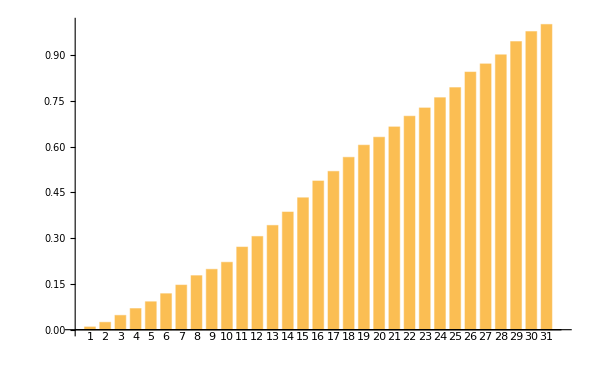

```mathematica
BarChart[Accumulate[arcs]/Total[arcs]//N,ChartLabels->Range[31]]
```

```mathematica
Sort@arcs
```

{15135,25411,34600,37369,37474,37850,38655,38869,43508,44139,44723,45308,47145,49838,51703,52506,54841,55233,56206,56560,57924,58640,60541,66684,72542,73498,77070,78154,83401,85143,91947}

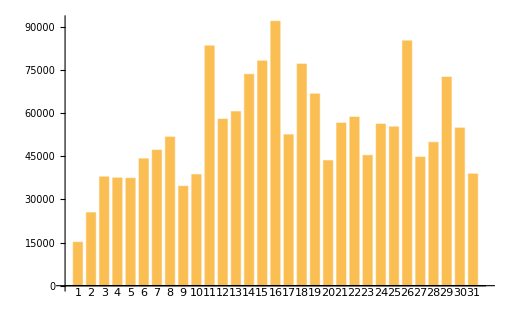

```mathematica
BarChart[arcs,ChartLabels->Range[31]]
```

```mathematica
%3[[-1]]/31.
```

53955.4

```mathematica
%3
```

```mathematica
15135+25411
```

40546

```mathematica
Accumulate/@{arcs[[;;6]],arcs[[7;;10]],arcs[[11;;14]],arcs[[15;;16]],arcs[[17;;19]],arcs[[20;;24]],arcs[[25;;27]],arcs[[28;;]]}
```

{{15135,40546,78396,115870,153239,197378},{47145,98848,133448,172103},{83401,141325,201866,275364},{78154,170101},{52506,129576,196260},{43508,100068,158708,204016,260222},{55233,140376,185099},{49838,122380,177221,216090}}

```mathematica
Last/@%
```

{197378,172103,275364,170101,196260,260222,185099,216090}

```mathematica
275364/185099.
```

1.48766

```mathematica
1084170./7
```

154881.

```mathematica
401189-185099
```

216090